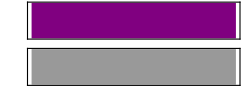

```mathematica
Sound[SoundNote[1]]
```

```mathematica
Sound[SoundNote[3]]
```

-Graphics-

```mathematica
EventHandler[InputField[],
{"KeyDown","q"}:>Speak["Q"],
{"KeyDown","w"}:>Speak["W"],
{"KeyDown","e"}:>Speak["E"],
{"KeyDown","r"}:>Speak["R"],
{"KeyDown","t"}:>Speak["T"],
{"KeyDown","y"}:>Speak["Y"],
{"KeyDown","u"}:>Speak["U"],
{"KeyDown","i"}:>Speak["I"],
{"KeyDown","o"}:>Speak["O"],
{"KeyDown","p"}:>Speak["P"]]
```

```mathematica
EmitSound[Sound[SoundNote["C"]]];
EmitSound[Sound[SoundNote["E"]]]
```

```mathematica
EventHandler[InputField[],
{"KeyDown","q"}:>EmitSound[Sound[SoundNote["C5",1,"Guitar"]]],{"KeyDown","w"}:>EmitSound[Sound[SoundNote["B",2,"Guitar"]]],{"KeyDown","e"}:>EmitSound[Sound[SoundNote["A",2,"Guitar"]]],{"KeyDown","r"}:>EmitSound[Sound[SoundNote["G",2,"Guitar"]]],{"KeyDown","t"}:>EmitSound[Sound[SoundNote["F",2,"Guitar"]]],{"KeyDown","y"}:>EmitSound[Sound[SoundNote["E",2,"Guitar"]]],{"KeyDown","u"}:>EmitSound[Sound[SoundNote["D",2,"Guitar"]]],{"KeyDown","i"}:>EmitSound[Sound[SoundNote["C",2,"Guitar"]]],{"KeyDown","o"}:>EmitSound[Sound[SoundNote["B3",2,"Guitar"]]],{"KeyDown","p"}:>EmitSound[Sound[SoundNote["A3",2,"Guitar"]]],{"KeyDown","a"}:>EmitSound[Sound[SoundNote["G3",2,"Guitar"]]],{"KeyDown","s"}:>EmitSound[Sound[SoundNote["F3",2,"Guitar"]]],{"KeyDown","d"}:>EmitSound[Sound[SoundNote["E3",2,"Guitar"]]],{"KeyDown","f"}:>EmitSound[Sound[SoundNote["D3",2,"Guitar"]]],{"KeyDown","g"}:>EmitSound[Sound[SoundNote["C3",2,"Guitar"]]]]
```